## B decays

Constants

```mathematica
v=  246 * 10^-3;
mt = 162.9* 10^-3;
mw = 80.377* 10^-3;
mc = mt * 0.003686;(*1.27* 10^-3;*)
sw2 = 0.2314;
mz = 91.1876* 10^-3;
Vcs = 0.97;
Vts = - 0.04;
fac=1/(4sw2)*mt^2/(4*mw^2)*v^2;
```

Wilson Coefficients

```mathematica
C10μ[CRRμμtt_,CLRμμtt_,CRRμμct_,CLRμμct_,Λ_]:=(CRRμμtt-CLRμμtt+(Vcs*mc/(Vts*mt))*(CRRμμct-CLRμμct))*fac*Log[Λ^2/mw^2]/Λ^2;
C10e[CRReett_,CLReett_,CRReect_,CLReect_,Λ_]:=(CRReett-CLReett+(Vcs*mc/(Vts*mt))*(CRReect-CLReect))*fac*Log[Λ^2/mw^2]/Λ^2;
C9μ[CRRμμtt_,CLRμμtt_,CRRμμct_,CLRμμct_,Λ_]:=(CRRμμtt+CLRμμtt+(Vcs*mc/(Vts*mt))*(CRRμμct+CLRμμct))*fac*Log[Λ^2/mw^2]/Λ^2;
C9e[CRReett_,CLReett_,CRReect_,CLReect_,Λ_]:=(CRReett+CLReett+(Vcs*mc/(Vts*mt))*(CRReect+CLReect))*fac*Log[Λ^2/mw^2]/Λ^2;
```

Chi-square Function

```mathematica
C9[CRRμμtt_,CLRμμtt_,CRRμμct_,CLRμμct_,CRReett_,CLReett_,CRReect_,CLReect_, Λ_]:= C9μ[CRRμμtt,CLRμμtt,CRRμμct,CLRμμct,Λ] - C9e[CRReett,CLReett,CRReect,CLReect,Λ];
```

```mathematica
COV = {{0.228^2, 0.293 * 0.228 * 0.683, 0.104 * 0.228 * 0.687}, {0.293 * 0.228 * 0.683, 0.683^2, -0.897 * 0.683 * 0.687}, {0.104 * 0.687 * 0.228, -0.897 * 0.683 * 0.687, 0.687^2}};
(*COV = {{1, 0.293, 0.104}, {0.293, 1, -0.897}, {0.104, -0.897, 1}};*)
```

```mathematica
Cvec[CRRμμtt_,CLRμμtt_,CRRμμct_,CLRμμct_,CRReett_,CLReett_,CRReect_,CLReect_, Λ_]:=
{C10μ[CRRμμtt,CLRμμtt,CRRμμct,CLRμμct,Λ] + 0.011,
C10e[CRReett,CLReett,CRReect,CLReect,Λ] - 0.469, 
 C9[CRRμμtt,CLRμμtt,CRRμμct,CLRμμct,CRReett,CLReett,CRReect,CLReect, Λ]+ 0.708 
};
```

```mathematica
χsqr[CRRμμtt_,CLRμμtt_,CRRμμct_,CLRμμct_,CRReett_,CLReett_,CRReect_,CLReect_, Λ_] :=
Cvec[CRRμμtt,CLRμμtt,CRRμμct,CLRμμct,CRReett,CLReett,CRReect,CLReect, Λ].Inverse[COV].Cvec[CRRμμtt,CLRμμtt,CRRμμct,CLRμμct,CRReett, CLReett,CRReect,CLReect, Λ];
```

Coefficient  Constraints

```mathematica
(*CeettLR*)
C$eett$LR$min=NMinimize[χsqr[0,0,0,0,0,x,0,0,1],{x}][[1]];
NSolve[{χsqr[0,0,0,0,0,1,0,0,Λ]-C$eett$LR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[0,0,0,0,0,-1,0,0,Λ]-C$eett$LR$min==4,0.2<Λ<10},{Λ}]
```

{{Λ→1.21292}}

{{Λ→3.17626}}

```mathematica
(*CeettRR*)
C$eett$RR$min=NMinimize[χsqr[0,0,0,0,x,0,0,0,1],{x}][[1]];
NSolve[{χsqr[0,0,0,0,1,0,0,0,Λ]-C$eett$RR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[0,0,0,0,-1,0,0,0,Λ]-C$eett$RR$min==4,0.2<Λ<10},{Λ}]
```

{{Λ→0.337198}}

{{Λ→0.527275}}

```mathematica
(*CeectLR*)
C$eect$LR$min=NMinimize[χsqr[0,0,0,0,0,0,0,x,1],{x}][[1]];
NSolve[{χsqr[0,0,0,0,0,0,0,1,Λ]-C$eect$LR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[0,0,0,0,0,0,0,-1,Λ]-C$eect$LR$min==4,0.2<Λ<10},{Λ}]
```

{{Λ→0.737268}}

{{Λ→0.221736}}

```mathematica
(*CeectRR*)
C$eect$RR$min=NMinimize[χsqr[0,0,0,0,0,0,1,0,x],{x}][[1]];
NSolve[{χsqr[0,0,0,0,0,0,1,0,Λ]-C$eect$RR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[0,0,0,0,0,0,-1,0,Λ]-C$eect$RR$min==4,0.2<Λ<10},{Λ}]
```

{}

{}

```mathematica
(*CμμttLR*)
C$μμtt$LR$min=NMinimize[χsqr[0,x,0,0,0,0,0,0,1],{x}][[1]];
NSolve[{χsqr[0,1,0,0,0,0,0,0,Λ]-C$μμtt$LR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[0,-1,0,0,0,0,0,0,Λ]-C$μμtt$LR$min==4,0.2<Λ<10},{Λ}]
```

{{Λ→3.27919}}

{{Λ→1.32514}}

```mathematica
(*CμμttRR*)
C$μμtt$RR$min=NMinimize[χsqr[x,0,0,0,0,0,0,0,1],{x}][[1]];
NSolve[{χsqr[1,0,0,0,0,0,0,0,Λ]-C$μμtt$RR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[-1,0,0,0,0,0,0,0,Λ]-C$μμtt$RR$min==4,0.2<Λ<10},{Λ}]
```

{{Λ→0.833903}}

{{Λ→0.925641}}

```mathematica
(*CμμctLR*)
C$μμct$LR$min=NMinimize[χsqr[0,0,0,x,0,0,0,0,1],{x}][[1]];
NSolve[{χsqr[0,0,0,1,0,0,0,0,Λ]-C$μμct$LR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[0,0,0,-1,0,0,0,0,Λ]-C$μμct$LR$min==4,0.2<Λ<10},{Λ}]
```

{{Λ→0.253739}}

{{Λ→0.763931}}

```mathematica
(*CμμctRR*)
C$μμct$RR$min=NMinimize[χsqr[0,0,x,0,0,0,0,0,1],{x}][[1]];
NSolve[{χsqr[0,0,1,0,0,0,0,0,Λ]-C$μμct$RR$min==4,0.2<Λ<10},{Λ}]
NSolve[{χsqr[0,0,-1,0,0,0,0,0,Λ]-C$μμct$RR$min==4,0.2<Λ<10},{Λ}]
```

{}

{}

```mathematica
C10μ[1,0,0,0,1]
```

0.338511

```mathematica
C$eett$LR$min=NMinimize[χsqr[0,0,0,0,0,1,0,0,x],{x}][[1]];
```

```mathematica
0.1525889797431213
```

0.152589

```mathematica
-6.593769669014715*^14
```

-6.59377×10^14

```mathematica
-1.199076103804071*^19
```

-1.19908×10^19

```mathematica
C$μμtt$LR$min=NMinimize[χsqr[0,1,0,0,0,0,0,0,x],{x}][[1]];
```

```mathematica
0.26100630760683674
```

0.261006

```mathematica
-3.116888405978207
```

-3.11689

```mathematica
NSolve[{χsqr[0,0,0,0,0,1,0,0,Λ]-C$eett$LR$min==4,0.2<Λ<10},{Λ}]
```

{{Λ→1.21292}}

```mathematica
NSolve[{χsqr[0,0,0,0,0,-1,0,0,Λ]-C$eett$LR$min=4,0.2<Λ<100000000000},{Λ}]
```

Set::write: Tag Plus in -0.79611+(0.011 (0.938406-56.3013 (-0.469+0.0671375 Power[«2»] Log[«1»])-53.1527 (0.708+0.0671375 Power[«2»] Log[«1»]))+(0.708+(«20» «1»)/Λ^2) («1»)+(-0.469+(0.0671375 Log[154.788 Power[«2»]])/Λ^2) (-0.619315+48.1281 (-0.469+0.0671375 Power[«2»] Log[«1»])+44.8628 (0.708+0.0671375 Power[«2»] Log[«1»]))) is Protected.

{}

```mathematica
χsqr[0,0,0,0,0,-1,0,0,100000000000000]
```

2.59213

```mathematica
C$eett$LR$min
```

0.79611

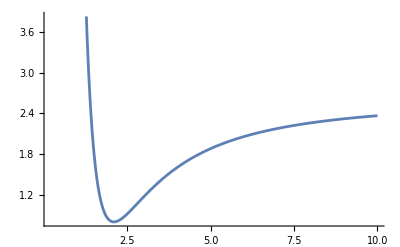

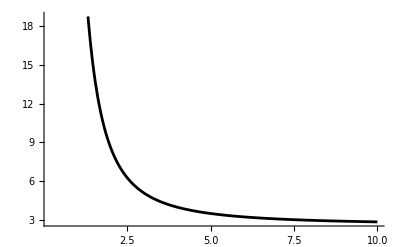

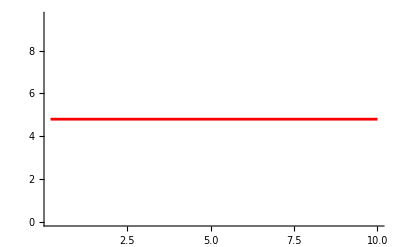

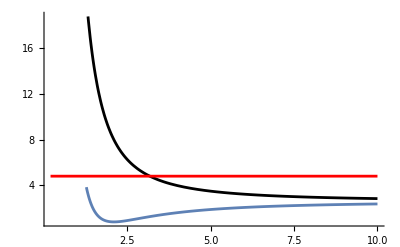

```mathematica
CeettLRPos=Plot[χsqr[0,0,0,0,0,1,0,0,x],{x,0.2,10}]
CeettLRNeg=Plot[χsqr[0,0,0,0,0,-1,0,0,x],{x,0.2,10},PlotStyle->Black]
CeettLRBound = Plot[4+C$eett$LR$min,{x,.2,10},PlotStyle->Red]
Show[CeettLRPos,CeettLRNeg,CeettLRBound,PlotRange->All]
```

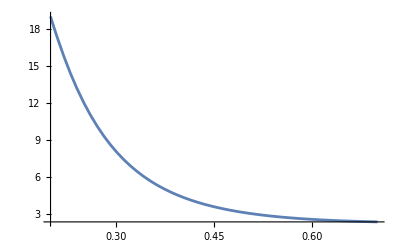

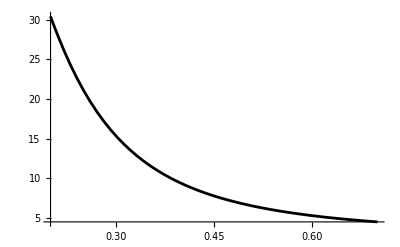

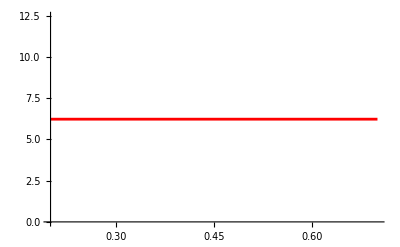

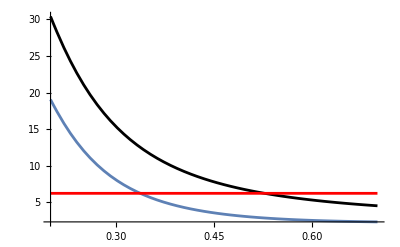

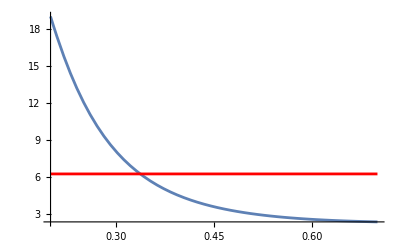

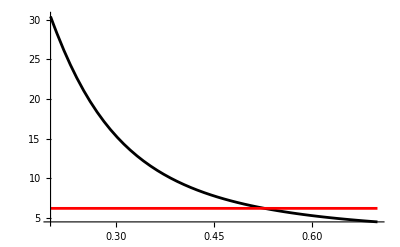

```mathematica
CeettRRPos=Plot[χsqr[0,0,0,0,1,0,0,0,x],{x,0.2,.7},PlotRange->All]
CeettRRNeg=Plot[χsqr[0,0,0,0,-1,0,0,0,x],{x,0.2,.7},PlotStyle->Black,PlotRange->All]
CeettRRBound = Plot[4+C$eett$RR$min,{x,.2,.7},PlotStyle->Red]
Show[CeettRRPos,CeettRRNeg,CeettRRBound,PlotRange->All]
Show[CeettRRPos,CeettRRBound,PlotRange->All]
Show[CeettRRNeg,CeettRRBound,PlotRange->All]
```

```mathematica
C9e[0,1,0,0,1]
```

0.338511

```mathematica
C9e[0,-1,0,0,1]
```

-0.338511

```mathematica
C9[0,0,0,0,0,-1,0,0,1]
```

0.338511

```mathematica
Inverse[COV]
```

{{85.3096,-56.3013,-53.1527},{-56.3013,48.1281,44.8628},{-53.1527,44.8628,43.961}}

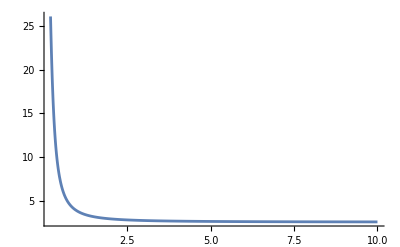

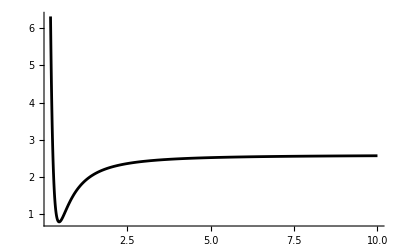

-Graphics-

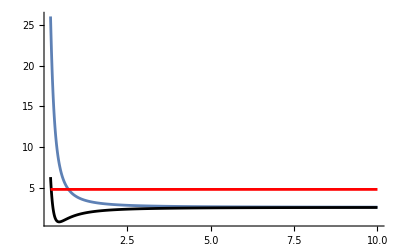

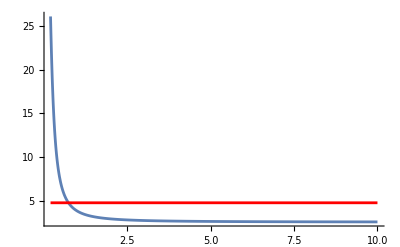

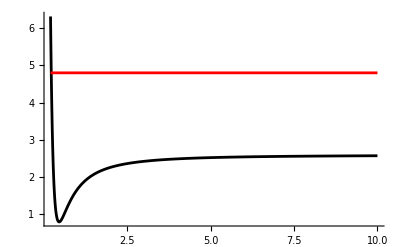

```mathematica
CeectLRPos=Plot[χsqr[0,0,0,0,0,0,0,1,x],{x,0.2,10},PlotRange->All]
CeectLRNeg=Plot[χsqr[0,0,0,0,0,0,0,-1,x],{x,0.2,10},PlotStyle->Black,PlotRange->All]
CeectLRBound = Plot[4+C$eect$LR$min,{x,.2,10},PlotStyle->Red]
Show[CeectLRPos,CeectLRNeg,CeectLRBound,PlotRange->All]
Show[CeectLRPos,CeectLRBound,PlotRange->All]
Show[CeectLRNeg,CeectLRBound,PlotRange->All]
```

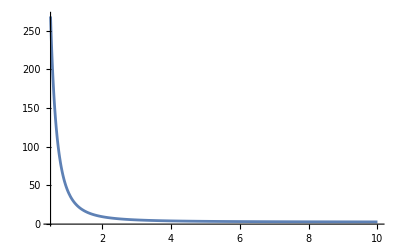

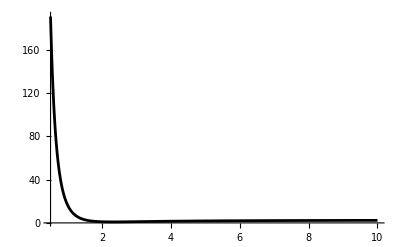

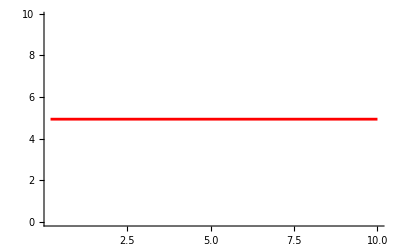

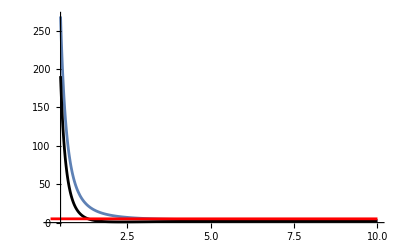

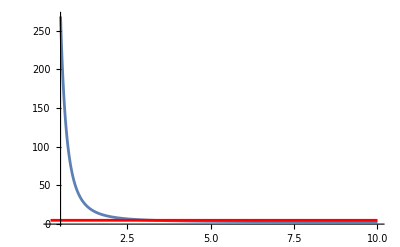

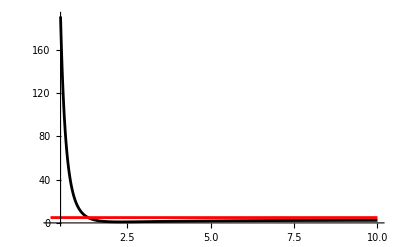

```mathematica
CμμttLRPos=Plot[χsqr[0,1,0,0,0,0,0,0,x],{x,0.5,10},PlotRange->All]
CμμttLRNeg=Plot[χsqr[0,-1,0,0,0,0,0,0,x],{x,0.5,10},PlotStyle->Black,PlotRange->All]
CμμttLRBound = Plot[4+C$μμtt$LR$min,{x,.2,10},PlotStyle->Red]
Show[CμμttLRPos,CμμttLRNeg,CμμttLRBound,PlotRange->All]
Show[CμμttLRPos,CμμttLRBound,PlotRange->All]
Show[CμμttLRNeg,CμμttLRBound,PlotRange->All]
```

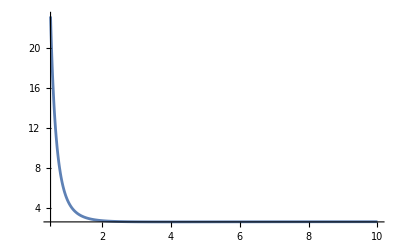

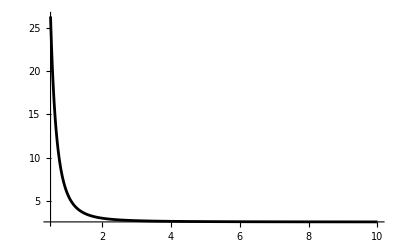

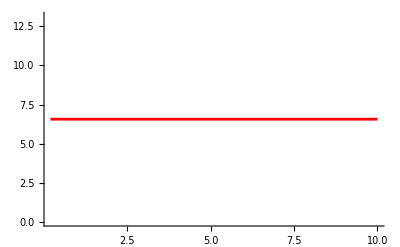

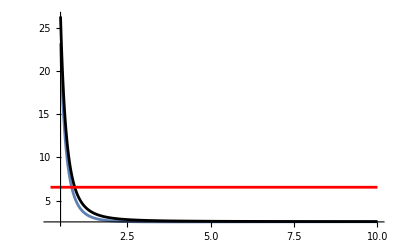

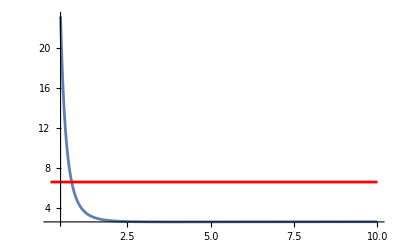

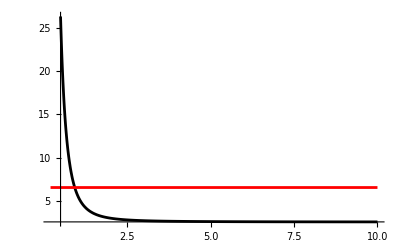

```mathematica
CμμttRRPos=Plot[χsqr[1,0,0,0,0,0,0,0,x],{x,0.5,10},PlotRange->All]
CμμttRRNeg=Plot[χsqr[-1,0,0,0,0,0,0,0,x],{x,0.5,10},PlotStyle->Black,PlotRange->All]
CμμttRRBound = Plot[4+C$μμtt$RR$min,{x,.2,10},PlotStyle->Red]
Show[CμμttRRPos,CμμttRRNeg,CμμttRRBound,PlotRange->All]
Show[CμμttRRPos,CμμttRRBound,PlotRange->All]
Show[CμμttRRNeg,CμμttRRBound,PlotRange->All]
```

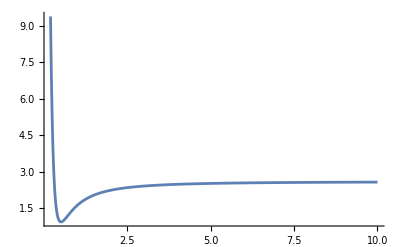

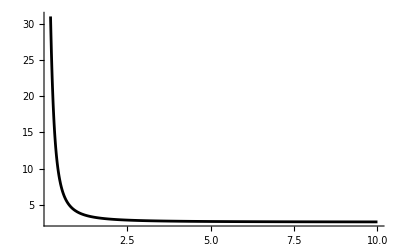

-Graphics-

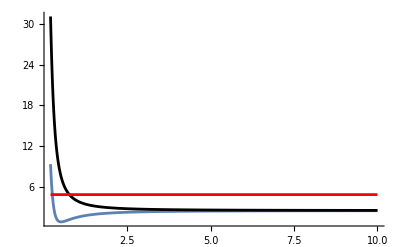

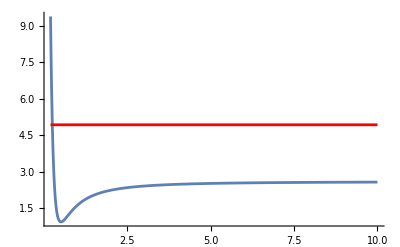

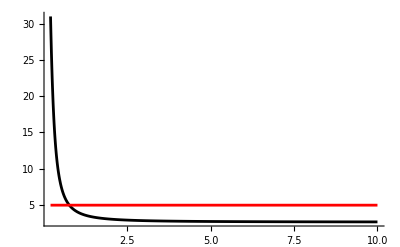

```mathematica
CμμctLRPos=Plot[χsqr[0,0,0,1,0,0,0,0,x],{x,0.2,10},PlotRange->All]
CμμctLRNeg=Plot[χsqr[0,0,0,-1,0,0,0,0,x],{x,0.2,10},PlotStyle->Black,PlotRange->All]
CμμctLRBound = Plot[4+C$μμct$LR$min,{x,.2,10},PlotStyle->Red]
Show[CμμctLRPos,CμμctLRNeg,CμμctLRBound,PlotRange->All]
Show[CμμctLRPos,CμμctLRBound,PlotRange->All]
Show[CμμctLRNeg,CμμctLRBound,PlotRange->All]
```

```mathematica
CμμctLRPos=Plot[χsqr[0,0,0,1,0,0,0,0,x],{x,0.2,10},PlotRange->All]
CμμctLRNeg=Plot[χsqr[0,0,0,-1,0,0,0,0,x],{x,0.2,10},PlotStyle->Black,PlotRange->All]
CμμctLRBound = Plot[4+C$μμct$LR$min,{x,.2,10},PlotStyle->Red]
Show[CμμctLRPos,CμμctLRNeg,CμμctLRBound,PlotRange->All]
Show[CμμctLRPos,CμμctLRBound,PlotRange->All]
Show[CμμctLRNeg,CμμctLRBound,PlotRange->All]CμμctLRPos=Plot[χsqr[0,0,0,1,0,0,0,0,x],{x,0.2,10},PlotRange->All]
CμμctLRNeg=Plot[χsqr[0,0,0,-1,0,0,0,0,x],{x,0.2,10},PlotStyle->Black,PlotRange->All]
CμμctLRBound = Plot[4+C$μμct$LR$min,{x,.2,10},PlotStyle->Red]
Show[CμμctLRPos,CμμctLRNeg,CμμctLRBound,PlotRange->All]
Show[CμμctLRPos,CμμctLRBound,PlotRange->All]
Show[CμμctLRNeg,CμμctLRBound,PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Set::write: Tag Times in   is Protected.

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-